# Mass Functions

This is a collection of routines to compute mass functions. 
Based on M. White, ApJS 2002

```mathematica
BeginPackage["Cosmology`MassFunction`"];

(* Needs statements go here *)
Needs["Cosmology`Defs`"];

(* You should put usage statements here *)
deltac::usage = "deltac is the spherical collapse overdensity; we keep this as a symbolic constant = 1.686";
ShethTormen::usage = "ShethTormen[v] is the Sheth-Tormen multiplicity function";
PressSchechter::usage = "PressSchechter[v] is the PS multiplicity function";
bias::usage = "bias[multiplicity, nu_] returns a bias given a multiplicity function";
```

```mathematica
(* The private section of the package is here *)
Begin["`Private`"];
```

## Multiplicity functions

We start by defining the multiplicity function :
	 \nu f(\nu) d\nu = \frac{M}{2 \bar{\rho}} \frac{dn}{dM} dM
where 
	\nu = \delta_c / \sigma(M)
Reorganizing the above somewhat, we get 
	 = dn/dM = (2 \bar{\rho} / M)  \nu^2 f(\nu) (d \ln(\nu)/ dM) =  -  (2 \bar{\rho} / M)  \nu^2 f(\nu) (d \sigma(M)/ dM)

Below, we define a number of these multiplicity functions - Press-Schechter and Sheth-Tormen as well as code to compute sigma(M) and its derivatives to get the mass function. Note that
we define the multiplicity function to by \nu f(\nu)

```mathematica
(* Generic functional form *)
vfv[v_] := norm*(1 + (a*v^2)^(-p)) * Exp[- a*v^2/2] / Sqrt[a];
ShethTormen[v_] := vfv[v] /. {a -> 0.707, p-> 0.3, norm-> 1/(2*5.50221)};
PressSchechter[v_] := vfv[v]/.{a->1, p->0, norm-> 1/Sqrt[8 Pi]};
```

## Bias

Within the peak background split, the bias may be calculated by differentiation ln (dn/dM) with respect to delta_c. This is more conveniently done by using 
	d \nu/ d \delta_c =  \nu / \delta_c
Note that the way we have written the above expressions, only \nu^2 f(\nu) depends on \delta_c

```mathematica
bias[multiplicity_, nu_] := Module[{x}, 
	1 + Simplify[D[Log[x * multiplicity[x]], x]] * (-x / deltac)/. {x-> nu}
];
```

Note that the 1+ term above is to convert to Eulerian bias.

### Normalization

The normalization of the multiplicity function νf(ν) is normalized such that ∫νf(ν) dν = 1/2. We explicitly test this below (the normalizations above were adjusted so that this is true).

```mathematica
Integrate[PressSchechter[v],{v,0, Infinity}]
```

1/2

Note that the ShethTormen normalization is a floating point number....

```mathematica
Integrate[ShethTormen[v], {v, 0, Infinity}]
```

0.5

```mathematica
End[];
EndPackage[];
```

## Testing

```mathematica
bPS[x_]:=bias[PressSchechter, x] /. {deltac -> 1.686};
```

```mathematica
bST[x_]:=bias[ShethTormen, x] /. {deltac -> 1.686};
```

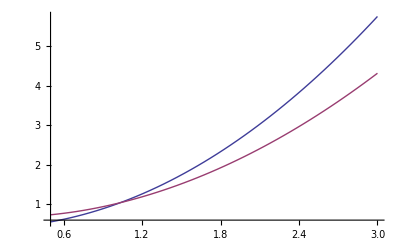

```mathematica
Plot[{bPS[x], bST[x]}, {x, 0.5, 3.0}]
```